## Paquetes y definiciones para este cuaderno

```mathematica
(* Set directory to this notebook's directory *)
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/QMB.wl"]
```

```mathematica
(* Operador de evolución *)
U[H_,t_]:=MatrixExp[-I*H*t]
```

## Cálculos

```mathematica
(* Número de espines *)
L=7;

(* Hamiltoniano de Ising (cadena de Wisniacki) *)
H=IsingNNOpenHamiltonian[1.,2.5,1.,L];

(* Estado inicial del entorno *)
ψ=RandomChainProductState[L-1];
```

Expresión analítica de la pureza de la matriz de Choi:

```mathematica
Chop[Purity[MatrixPartialTrace[#.(KroneckerProduct[Pauli[0]/2,Dyad[ψ]]).ConjugateTranspose[#]&[MatrixExp[-I H]],1,2]]]
```

0.548706

```mathematica
Chop[Tr[KroneckerProduct[#,#].KroneckerProduct[KroneckerProduct[Pauli[0]/2,Dyad[ψ]],KroneckerProduct[Pauli[0]/2,Dyad[ψ]]].KroneckerProduct[ConjugateTranspose[#],ConjugateTranspose[#]]&[MatrixExp[-I H]].PermutationMatrix[p]]]
```

```mathematica
1/12(3Pauli[{0,0}]+Pauli[{1,1}]+Pauli[{2,2}]+Pauli[{3,3}])//MatrixForm
```

(1/3 | 0 | 0 | 0
0 | 1/6 | 1/6 | 0
0 | 1/6 | 1/6 | 0
0 | 0 | 0 | 1/3)

```mathematica
Psym=1/6(IdentityMatrix[4]+PermutationMatrix[{1,3,2,4}])
```

{{1/3,0,0,0},{0,1/6,1/6,0},{0,1/6,1/6,0},{0,0,0,1/3}}

```mathematica
L=2;p2=Flatten[Position[Tuples[{0,1},2L],{#[[1]],#[[3]],#[[2]],#[[4]]}]&/@Tuples[{0,1},2L]]
```

{1,2,5,6,3,4,7,8,9,10,13,14,11,12,15,16}

```mathematica
KroneckerProduct[Psym,Psym]//MatrixForm
```

(1/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/18 | 1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/18 | 1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/36 | 1/36 | 0 | 0 | 1/36 | 1/36 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/36 | 1/36 | 0 | 0 | 1/36 | 1/36 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/36 | 1/36 | 0 | 0 | 1/36 | 1/36 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/36 | 1/36 | 0 | 0 | 1/36 | 1/36 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/9 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/9)

```mathematica
PermutationMatrix[p2].KroneckerProduct[Psym,Psym].ConjugateTranspose[PermutationMatrix[p2]]//MatrixForm
```

(1/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/18 | 0 | 0 | 1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/18 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 0
0 | 1/18 | 0 | 0 | 1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0
0 | 0 | 1/18 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/9 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0 | 1/18 | 0
0 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 1/36 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 0 | 1/18 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/9)

```mathematica
Chop/@{Tr[MatrixPartialTrace[U[H,1.2].KroneckerProduct[Dyad[{1,0}],Dyad[ψ]].ConjugateTranspose[U[H,1.2]],1,{2,4}].MatrixPartialTrace[U[H,1.2].KroneckerProduct[Dyad[{0,1}],Dyad[ψ]].ConjugateTranspose[U[H,1.2]],1,{2,4}]],Tr[MatrixPartialTrace[U[H,1.2].KroneckerProduct[Dyad[{1,0}],Dyad[ψ]].ConjugateTranspose[U[H,1.2]],2,{2,4}].MatrixPartialTrace[U[H,1.2].KroneckerProduct[Dyad[{0,1}],Dyad[ψ]].ConjugateTranspose[U[H,1.2]],2,{2,4}]]}
```

{0.347595,0.59828}

```mathematica
t=0.3;
Purity[MatrixPartialTrace[U[H,t].KroneckerProduct[Dyad[{1,0}],Dyad[ψ]].ConjugateTranspose[U[H,t]],1,{2,4}]]-2Tr[MatrixPartialTrace[U[H,t].KroneckerProduct[Dyad[{1,0}],Dyad[ψ]].ConjugateTranspose[U[H,t]],1,{2,4}].MatrixPartialTrace[U[H,t].KroneckerProduct[Dyad[{0,1}],Dyad[ψ]].ConjugateTranspose[U[H,t]],1,{2,4}]]+Purity[MatrixPartialTrace[U[H,t].KroneckerProduct[Dyad[{0,1}],Dyad[ψ]].ConjugateTranspose[U[H,t]],1,{2,4}]]//Chop
```

0.538566

```mathematica
Purity[MatrixPartialTrace[U[H,10.2].KroneckerProduct[Dyad[Normalize[{1,1}]],Dyad[ψ]].ConjugateTranspose[U[H,10.2]],1,{2,4}]]
```

0.604159-1.10254×10^-17 ⅈ

```mathematica
t=0.3;Tr[MatrixPartialTrace[U[H,t].KroneckerProduct[Dyad[{1,0}],Dyad[ψ]].ConjugateTranspose[U[H,t]],1,{2,4}].MatrixPartialTrace[U[H,t].KroneckerProduct[Dyad[{0,1}],Dyad[ψ]].ConjugateTranspose[U[H,t]],1,{2,4}]]
```

0.716665+0. ⅈ

```mathematica
1/12.
```

0.0833333

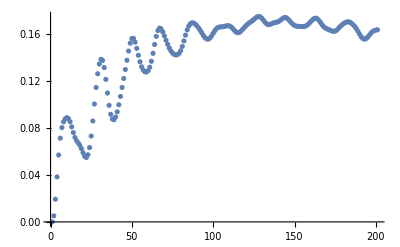

```mathematica
Table[1/12.Total[Purity[MatrixPartialTrace[U[H,t].KroneckerProduct[Pauli[#],Dyad[ψ]].ConjugateTranspose[U[H,t]],1,{2,2^(L-1)}]]&/@{1,2,3}]//Chop,{t,0,20,0.1}]//ListPlot
```